Converge of the numerical scheme

In the file “data_Gamma=1._d=1._gamma=0.02_precision _ 20.txt” we saved dependence of the absorption coefficient A_n on the dimensional frequency obtained from the numerical scheme at the different number of functions n=1,...,10. In the figure we we present dependence ΔA_n=A_n-A_(n-1) at n=10,8,6. Thus with the number n increasing, difference ΔA_n approaches to zero.

```mathematica
mas=Get[NotebookDirectory[]<>"data_Gamma=1._d=1._gamma=0.02_precision_20.txt"];
```

```mathematica
acc=Module[{L=Length[mas],M=Length[mas[[1,2]]]},
Table[{mas[[n,2,m,1]],mas[[n,2,m,2]]-mas[[n-1,2,m,2]]},{n,2,L},{m,1,M}]
];
```

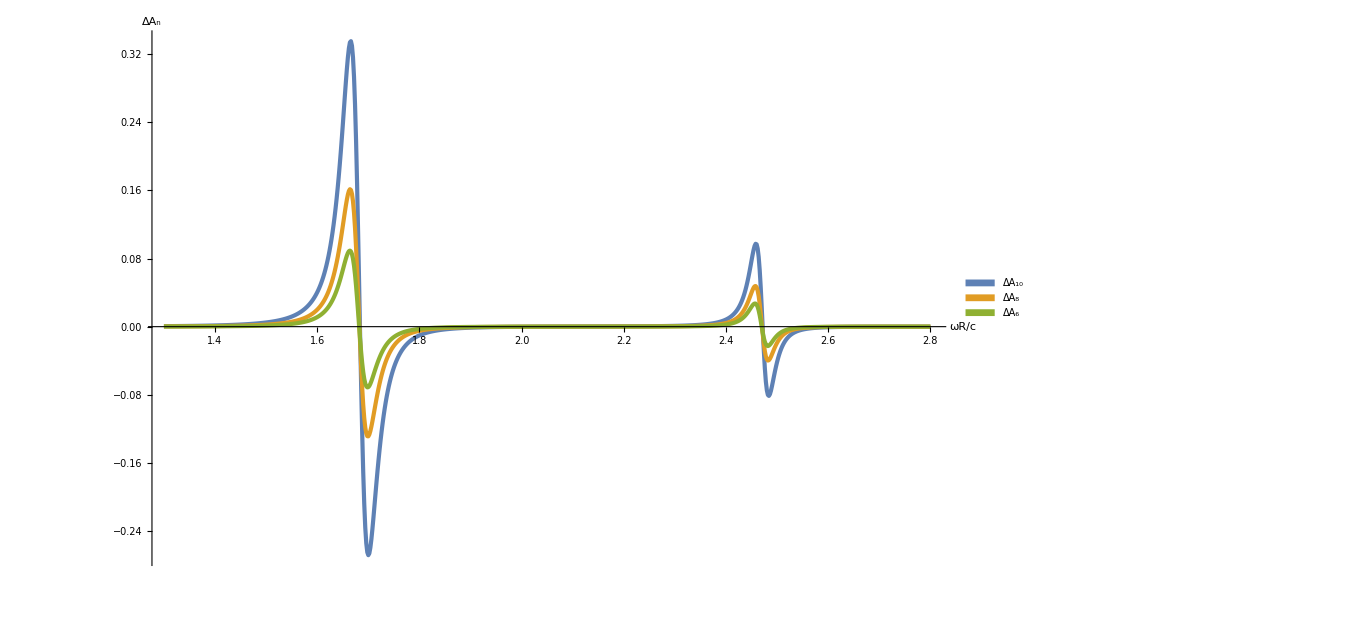

```mathematica
fl[text_]:=Text[Style[text,Italic,45,FontFamily->"Times"]];
ListLinePlot[{acc[[5]],acc[[7]],acc[[9]]},PlotRange->All,ImageSize->1000,Frame->False,TicksStyle->Directive[Black,Thick],LabelStyle->{FontSize->30,FontFamily->"Calibri",FontColor->Black},AxesStyle->Directive[Thickness[0.002],Black],AxesLabel->{fl["ωR/c"],fl["ΔA_n"]},PlotStyle->{Thickness[0.003]},PlotLegends->SwatchLegend[{"ΔA_10","ΔA_8","ΔA_6"}]]
```